Failure[…]

Failure[…]

```mathematica
Probability[x==3,x\[Distributed]DiscreteUniformDistribution[{1,6}]] (* \[Distributed] Esc dist Esc *)
```

1/6

```mathematica
Probability[x+y ==12,x\[Distributed]DiscreteUniformDistribution[{1,6}] && y\[Distributed]DiscreteUniformDistribution[{1,6}]]
```

1/36

```mathematica
probs =Table[
	Probability[x+y == result,x\[Distributed]DiscreteUniformDistribution[{1,6}] && y\[Distributed]DiscreteUniformDistribution[{1,6}]],	
	{result,2,12,1}
]
```

{1/36,1/18,1/12,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36}

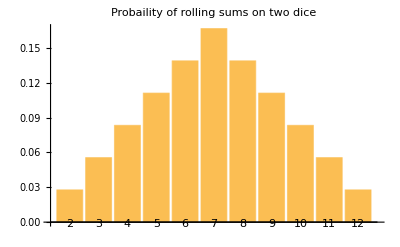

```mathematica
BarChart[
	probs,
	ChartLabels->Table[i,{i,2,12,1}],
	PlotLabel->"Probaility of rolling sums on two dice"
]
```

```mathematica
(* 与分布联合使用 *)
PDF[DiscreteUniformDistribution[{0,6}],x]
```

Piecewise[{{1/7, 0≤x≤6}, {0, True}}]

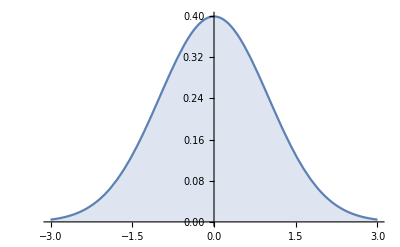

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-3,3},Filling->Axis]
```

```mathematica
myFunc[x_] :=PDF[NormalDistribution[0,1],x]
```

```mathematica
myFunc[0]
```

1/(√(2 π))

```mathematica
points = Table[{x,myFunc[x]},{x,-3,3,1}];
```

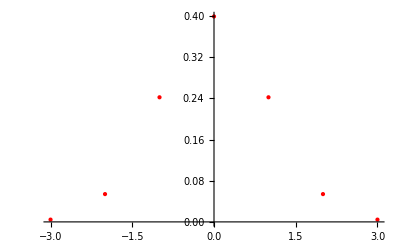

```mathematica
ListPlot[points,PlotStyle->{Red,PointSize[Medium]}]
```

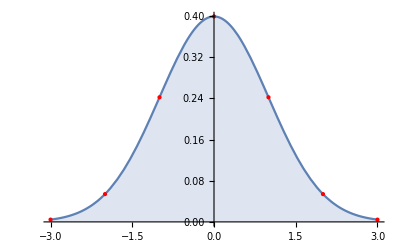

```mathematica
Show[Plot[myFunc[x],{x,-3,3},Filling->Axis],ListPlot[points,PlotStyle->{Red,PointSize[Medium]}]]
```

```mathematica
(* 使用Manipulate探索均值和标准差对正态分布的影响 *)
Manipulate[
	Plot[PDF[NormalDistribution[mean,var],x],{x,-10,10},Filling->Bottom],
	{mean,-10,10},
	{var, 1,10}
]
```

```mathematica
(* 统计 *)
data = {1,2,2,3,3,3,4,4,4,4,5,5,5,5,5};
```

```mathematica
Mean[data]
```

11/3

```mathematica
Median[data]
```

4

```mathematica
Commonest[data](* 众数 *)
```

{5}

```mathematica
Mean[{p1,p2,p3,p4,p5}]
```

1/5 (p1+p2+p3+p4+p5)

```mathematica
Commonest[{x,x^2,x^2,x^3,x^3,x^3}]
```

{x^3}

```mathematica
data = {1,2,2,3,3,3,4,4,4,4,5,5,5,5,5};
```

```mathematica
Variance[data]
```

5/3

```mathematica
StandardDeviation[data]
```

√(5/3)

```mathematica
InterquartileRange[data]
```

2

```mathematica
(* 相关系数 *)
list1 = {1,2,2,3,3,3,4,4,4,4,5,5,5,5,5};
list2 = {1,2,3,4,5,6,7,8,9,8,7,6,5,4,3};
```

```mathematica
Covariance[list1,list2]
```

23/14

```mathematica
Correlation[list1,list2]
```

(23 √(3/7))/28

```mathematica
(* 曲线拟合 *)
myData =  CountryData["Iceland",{{"GDP"},{1970,2010}}]
```

TimeSeries[…]

```mathematica
myData["Values"]
```

QuantityArray[…]

```mathematica
QuantityMagnitude[myData["Values"]]
```

{5.26705×10^8,6.70251×10^8,8.39652×10^8,1.15444×10^9,1.51519×10^9,1.40688×10^9,1.66949×10^9,2.20851×10^9,2.51183×10^9,2.85344×10^9,3.38142×10^9,3.493×10^9,3.20663×10^9,2.76595×10^9,2.86444×10^9,2.98405×10^9,3.98962×10^9,5.52032×10^9,6.10664×10^9,5.67257×10^9,6.46874×10^9,6.90973×10^9,7.08098×10^9,6.21858×10^9,6.38946×10^9,7.12363×10^9,7.42608×10^9,7.56967×10^9,8.50369×10^9,8.98205×10^9,9.02566×10^9,8.23485×10^9,9.3184×10^9,1.14293×10^10,1.38253×10^10,1.6853×10^10,1.74653×10^10,2.16525×10^10,1.80746×10^10,1.31544×10^10,1.37512×10^10}

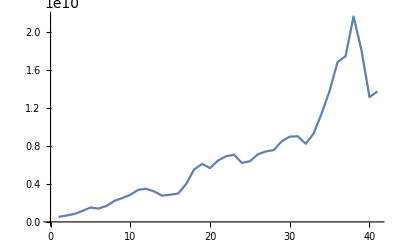

```mathematica
myData = QuantityMagnitude[myData["Values"]];
ListLinePlot[myData] (* 冰岛GDP数据可视化 *)
```

```mathematica
(* 构造模型并且拟合冰岛GDP随时间发展规律 *)
myModel = LinearModelFit[myData,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x] (* 第二个参数制定了模型的容量表示其线性模型的基 *);
```

```mathematica
myModel[1]
```

8.11407×10^8

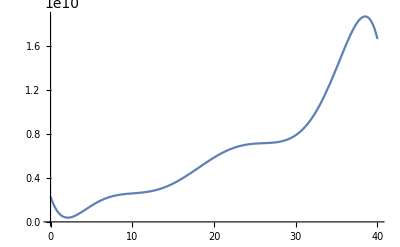

```mathematica
Plot[myModel[x],{x,0,40}]
```

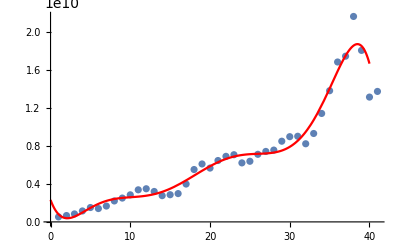

```mathematica
Show[ListPlot[myData],Plot[myModel[x],{x,0,40},PlotStyle->Red]]
```

```mathematica
(* 返回最优拟合曲线表达式 *)
TraditionalForm[myModel["BestFit"]]
```

0.270333 x^8-91.0797 x^7+9151.83 x^6-424829. x^5+1.03262×10^7 x^4-1.33829×10^8 x^3+8.76324×10^8 x^2-2.25679×10^9 x+2.31579×10^9

```mathematica
(* 获取完整的属性列表 *)
Short[myModel["Properties"]]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,«55»,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
myModel["AdjustedRSquared"]
```

0.956858

GraphicsGrid::list: {,} is not a list of lists.

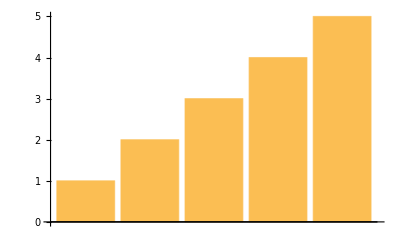
GraphicsGrid[{-Graphics-,-Graphics3D-},{-Graphics-,-Graphics3D-}]

```mathematica
(* 统计可视化 *)
data = {1,2,3,4,5};
GraphicsGrid[
	{BarChart[data],BarChart3D[data]},
	{PieChart[data],PieChart3D[data]}	

](* 用于并列画出多种统计图表的东西，类似于Show *)
```

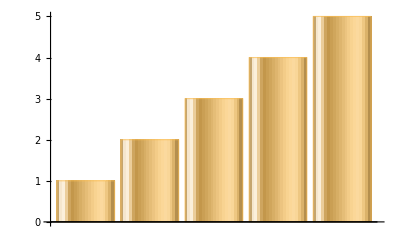

```mathematica
BarChart[data,ChartElementFunction->"GlassRectangle"]
```

{{4,4,4,1,4},{2,0,4,3,2},{1,4,4,2,1},{0,0,4,3,0}}

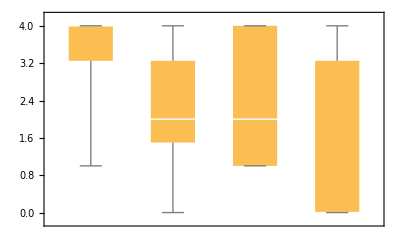

```mathematica
boxData = RandomInteger[{0,4},{4,5}]
BoxWhiskerChart[boxData]
```

```mathematica
Clear[probs,myFunc,myData,myModel,points,data,list1,list2,boxData]
```